```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_ETH/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | eth Price | log return future | log return eth
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 2784.74 | 0.0212907 | 0.068794
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 2599.61 | -0.0904653 | -0.269777
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 3404.63 | -0.0196938 | 0.00767698
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 3378.6 | -0.131645 | -0.18102
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 4049.04 | 0.03685 | 0.103942
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 3649.31 | -0.119603 | -0.11274
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 4084.82 | -0.042369 | 0.0033428
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 4071.19 | 0.018947 | 0.0196738
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 3991.88 | -0.0359909 | 0.127305)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return eth

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=89, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

89

88

87

86

85

84

83

82

81

80

79

78

77

76

75

74

73

72

71

70

69

68

67

66

65

64

63

62

61

60

59

58

57

56

55

54

53

52

51

50

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1.25331/(1.09180814843873×10^345) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.733333-10. F2NIG2(«1»))^2+(0.533333-«19» («1»))^2+(0.333333-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$152772398,β$152772398} = {28.2964,2.18771}.

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

NMinimize::nnum: The function value √((0.6-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.7-10. F2NIG2(InverseCDF[«22»[«5»],0.1],«6»,«21»[«1»]))^2+(«1»)^2+(0.4-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$182745727,β$182745727} = {28.2964,2.18771}.

12

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.7-10. F2NIG2(InverseCDF[«22»[«5»],0.1],«7»))^2+(0.5-«19» «1»)^2+(0.4-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$183191269,β$183191269} = {28.2964,2.18771}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{0.866957,-0.389032}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_Tiingo_ETH/

```mathematica
For[kk=0, kk≤111, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.996490606758976}. NIntegrate obtained 0.107808 and 0.000156419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.996490606758976}. NIntegrate obtained 0.10478 and 0.000238933 for the integral and error estimates.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.996490606758976}. NIntegrate obtained 0.106774 and 0.00014753 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.564556 | 0.310452 | 0.43625 | 0.244452 | 0.333157 | 0.374721
 | 2021-05-13 | 0.565796 | 0.34771 | 0.455293 | 0.312162 | 0.365539 | 0.352897
 | 2021-05-06 | 0.57719 | 0.362532 | 0.442635 | 0.323498 | 0.372193 | 0.365485
 | 2021-04-29 | 0.588512 | 0.377464 | 0.44328 | 0.339057 | 0.377555 | 0.368145
 | 2021-04-22 | 0.602979 | 0.383203 | 0.456716 | 0.344992 | 0.389886 | 0.383275
 | 2021-04-15 | 0.612246 | 0.399685 | 0.430479 | 0.369941 | 0.392742 | 0.394449
 | 2021-04-08 | 0.61168 | 0.401784 | 0.430377 | 0.371041 | 0.392516 | 0.392821
 | 2021-04-01 | 0.612903 | 0.407005 | 0.41695 | 0.402893 | 0.396551 | 0.404787
 | 2021-03-25 | 0.618349 | 0.415009 | 0.42222 | 0.408237 | 0.403364 | 0.376757
 | 2021-03-18 | 0.615634 | 0.407332 | 0.420102 | 0.404645 | 0.398776 | 0.407245
 | 2021-03-11 | 0.617329 | 0.406957 | 0.418643 | 0.40579 | 0.39837 | 0.411591
 | 2021-03-04 | 0.630696 | 0.410859 | 0.425035 | 0.398929 | 0.404339 | 0.42007
 | 2021-02-25 | 0.613779 | 0.405298 | 0.403832 | 0.4018 | 0.394116 | 0.408028
 | 2021-02-18 | 0.614274 | 0.43785 | 0.405306 | 0.407626 | 0.39067 | 0.410397
 | 2021-02-10 | 0.633327 | 0.44876 | 0.430501 | 0.423947 | 0.40941 | 0.421747
 | 2021-02-03 | 0.645334 | 0.470614 | 0.44706 | 0.44976 | 0.431668 | 0.423466
 | 2021-01-27 | 0.668112 | 0.464659 | 0.473977 | 0.42515 | 0.438465 | 0.442772
 | 2021-01-20 | 0.651161 | 0.474461 | 0.451627 | 0.452738 | 0.436038 | 0.428977
 | 2021-01-12 | 0.663662 | 0.457113 | 0.479827 | 0.410873 | 0.428681 | 0.446523
 | 2021-01-05 | 0.640023 | 0.464375 | 0.434746 | 0.405138 | 0.416665 | 0.437306
 | 2020-12-28 | 0.650172 | 0.45631 | 0.419475 | 0.394208 | 0.411113 | 0.445967
 | 2020-12-18 | 0.65276 | 0.470583 | 0.43358 | 0.4092 | 0.424158 | 0.425629
 | 2020-12-11 | 0.656349 | 0.471208 | 0.431554 | 0.406586 | 0.428778 | 0.42573
 | 2020-12-04 | 0.655593 | 0.475027 | 0.440616 | 0.407726 | 0.430703 | 0.422197
 | 2020-11-27 | 0.62704 | 0.507713 | 0.460938 | 0.445151 | 0.428243 | 0.396834
 | 2020-11-19 | 0.642994 | 0.550594 | 0.449643 | 0.427013 | 0.442314 | 0.394426
 | 2020-11-12 | 0.640302 | 0.520757 | 0.405195 | 0.41333 | 0.425874 | 0.399519
 | 2020-11-05 | 0.65037 | 0.522612 | 0.409724 | 0.418388 | 0.429616 | 0.413455
 | 2020-10-29 | 0.627946 | 0.506192 | 0.470563 | 0.442382 | 0.422662 | 0.392904
 | 2020-10-22 | 0.62856 | 0.516013 | 0.480108 | 0.443233 | 0.425593 | 0.39063
 | 2020-10-15 | 0.617444 | 0.502798 | 0.473897 | 0.438982 | 0.42019 | 0.374928
 | 2020-10-08 | 0.614012 | 0.496485 | 0.463105 | 0.432823 | 0.410498 | 0.377562
 | 2020-10-01 | 0.610014 | 0.493114 | 0.458657 | 0.430272 | 0.40707 | 0.37603
 | 2020-09-24 | 0.612714 | 0.495139 | 0.463589 | 0.432238 | 0.410645 | 0.376247
 | 2020-09-17 | 0.618322 | 0.465012 | 0.457224 | 0.43346 | 0.421545 | 0.378077
 | 2020-09-10 | 0.640744 | 0.485541 | 0.461031 | 0.44905 | 0.435593 | 0.400628
 | 2020-09-02 | 0.667754 | 0.535741 | 0.562542 | 0.419103 | 0.483668 | 0.393892
 | 2020-08-26 | 0.659323 | 0.521801 | 0.522535 | 0.403433 | 0.463681 | 0.405741
 | 2020-08-19 | 0.650238 | 0.507896 | 0.489709 | 0.38982 | 0.446581 | 0.409316
 | 2020-08-12 | 0.654154 | 0.518626 | 0.511407 | 0.400516 | 0.459308 | 0.402592
 | 2020-08-05 | 0.667144 | 0.510414 | 0.56737 | 0.408194 | 0.468545 | 0.41853
 | 2020-07-29 | 0.670844 | 0.525213 | 0.540692 | 0.411594 | 0.470114 | 0.420889
 | 2020-07-22 | 0.66633 | 0.519412 | 0.519404 | 0.40838 | 0.463427 | 0.40551
 | 2020-07-15 | 0.659482 | 0.484876 | 0.496831 | 0.386432 | 0.437489 | 0.415387
 | 2020-07-08 | 0.652598 | 0.480692 | 0.490485 | 0.381013 | 0.430857 | 0.408062
 | 2020-06-30 | 0.647131 | 0.496655 | 0.504836 | 0.382832 | 0.441364 | 0.398771
 | 2020-06-23 | 0.644797 | 0.483197 | 0.481818 | 0.379741 | 0.429274 | 0.396248
 | 2020-06-16 | 0.647092 | 0.483197 | 0.474414 | 0.380806 | 0.427093 | 0.412006
 | 2020-06-09 | 0.655315 | 0.474328 | 0.486391 | 0.376941 | 0.425119 | 0.419717
 | 2020-06-02 | 0.658606 | 0.478558 | 0.476754 | 0.383206 | 0.432456 | 0.416544
 | 2020-05-26 | 0.659551 | 0.475337 | 0.466609 | 0.381533 | 0.424909 | 0.43628
 | 2020-05-18 | 0.648822 | 0.483962 | 0.494172 | 0.3804 | 0.434345 | 0.413125
 | 2020-05-11 | 0.64209 | 0.470886 | 0.48027 | 0.366885 | 0.422563 | 0.412964
 | 2020-05-04 | 0.647929 | 0.477727 | 0.481805 | 0.374217 | 0.414305 | 0.430742
 | 2020-04-27 | 0.66013 | 0.502626 | 0.498852 | 0.39246 | 0.437688 | 0.427143
 | 2020-04-20 | 0.652063 | 0.482341 | 0.472338 | 0.378109 | 0.418019 | 0.429904
 | 2020-04-13 | 0.639159 | 0.481239 | 0.482217 | 0.369647 | 0.419848 | 0.409386
 | 2020-04-03 | 0.645248 | 0.485742 | 0.483887 | 0.378053 | 0.421864 | 0.415498
 | 2020-03-27 | 0.638111 | 0.479616 | 0.47122 | 0.368384 | 0.41542 | 0.414885
 | 2020-03-20 | 0.636834 | 0.479769 | 0.468399 | 0.369619 | 0.415033 | 0.413366
 | 2020-03-13 | 0.611139 | 0.456054 | 0.446044 | 0.353544 | 0.394335 | 0.386794
 | 2020-03-06 | 0.597178 | 0.426827 | 0.485438 | 0.319065 | 0.376556 | 0.391303
 | 2020-02-28 | 0.6252 | 0.434731 | 0.477134 | 0.329046 | 0.380176 | 0.42131
 | 2020-02-21 | 0.617643 | 0.437665 | 0.507265 | 0.324497 | 0.389748 | 0.41888
 | 2020-02-13 | 0.597247 | 0.433656 | 0.484361 | 0.326426 | 0.379406 | 0.396109
 | 2020-02-06 | 0.617687 | 0.441964 | 0.454029 | 0.352135 | 0.381311 | 0.419127
 | 2020-01-30 | 0.640107 | 0.427292 | 0.472657 | 0.336141 | 0.39626 | 0.431504
 | 2020-01-23 | 0.618178 | 0.401829 | 0.496078 | 0.300333 | 0.402187 | 0.396295
 | 2020-01-15 | 0.616125 | 0.400325 | 0.501195 | 0.295176 | 0.402192 | 0.395035
 | 2020-01-08 | 0.63713 | 0.398309 | 0.477802 | 0.29961 | 0.397198 | 0.423402
 | 2019-12-31 | 0.615166 | 0.395095 | 0.491411 | 0.292598 | 0.396815 | 0.393428
 | 2019-12-23 | 0.632569 | 0.39256 | 0.481745 | 0.291212 | 0.380097 | 0.429046
 | 2019-12-16 | 0.607711 | 0.384662 | 0.479712 | 0.290268 | 0.393385 | 0.383495
 | 2019-12-09 | 0.605913 | 0.384841 | 0.486543 | 0.288187 | 0.395792 | 0.382335
 | 2019-12-02 | 0.604243 | 0.372071 | 0.484668 | 0.286284 | 0.387618 | 0.378562
 | 2019-11-22 | 0.608121 | 0.374003 | 0.482751 | 0.285213 | 0.387477 | 0.386112
 | 2019-11-15 | 0.576819 | 0.353453 | 0.488486 | 0.272074 | 0.3733 | 0.356143
 | 2019-11-08 | 0.596106 | 0.347933 | 0.476661 | 0.268679 | 0.374242 | 0.374448
 | 2019-11-01 | 0.630903 | 0.359838 | 0.478611 | 0.281101 | 0.381674 | 0.419523
 | 2019-10-25 | 0.62727 | 0.364942 | 0.490326 | 0.282726 | 0.390621 | 0.407157
 | 2019-10-18 | 0.611755 | 0.434072 | 0.47232 | 0.305799 | 0.384196 | 0.385915
 | 2019-10-11 | 0.613724 | 0.434759 | 0.481624 | 0.299903 | 0.387481 | 0.384481
 | 2019-10-04 | 0.612469 | 0.433292 | 0.485162 | 0.296052 | 0.387379 | 0.382446
 | 2019-09-27 | 0.614753 | 0.435764 | 0.481218 | 0.30063 | 0.387889 | 0.38781
 | 2019-09-20 | 0.607041 | 0.356649 | 0.428389 | 0.28974 | 0.365579 | 0.396195
 | 2019-09-13 | 0.633651 | 0.378861 | 0.43337 | 0.315539 | 0.38423 | 0.424375
 | 2019-09-06 | 0.648672 | 0.386627 | 0.436838 | 0.328355 | 0.393545 | 0.441867
 | 2019-08-29 | 0.657957 | 0.387646 | 0.449861 | 0.302214 | 0.389863 | 0.450391
 | 2019-08-22 | 0.662001 | 0.387869 | 0.441996 | 0.316936 | 0.390736 | 0.459361
 | 2019-08-15 | 0.673882 | 0.390021 | 0.461298 | 0.322804 | 0.398616 | 0.46908
 | 2019-08-08 | 0.671035 | 0.398205 | 0.456058 | 0.338922 | 0.41519 | 0.457487
 | 2019-08-01 | 0.667262 | 0.399719 | 0.461025 | 0.335097 | 0.415491 | 0.448701
 | 2019-07-25 | 0.670151 | 0.399933 | 0.490405 | 0.334343 | 0.416147 | 0.449221
 | 2019-07-18 | 0.675964 | 0.403282 | 0.492497 | 0.339005 | 0.420739 | 0.454548
 | 2019-07-11 | 0.676444 | 0.435301 | 0.449509 | 0.387316 | 0.41745 | 0.460435
 | 2019-07-03 | 0.667858 | 0.434376 | 0.459054 | 0.381693 | 0.416202 | 0.44549
 | 2019-06-26 | 0.691128 | 0.391308 | 0.474066 | 0.337199 | 0.401574 | 0.494547
 | 2019-06-19 | 0.694326 | 0.40076 | 0.479554 | 0.342255 | 0.4078 | 0.489361
 | 2019-06-12 | 0.694436 | 0.40472 | 0.488915 | 0.346393 | 0.415556 | 0.478446
 | 2019-06-05 | 0.700378 | 0.405 | 0.493951 | 0.343263 | 0.414928 | 0.483366
 | 2019-05-29 | 0.700638 | 0.398549 | 0.482675 | 0.346894 | 0.407843 | 0.485832
 | 2019-05-21 | 0.69421 | 0.385863 | 0.480392 | 0.339134 | 0.40295 | 0.474991
 | 2019-05-14 | 0.713411 | 0.408076 | 0.48937 | 0.354845 | 0.425804 | 0.492851
 | 2019-05-07 | 0.713198 | 0.440842 | 0.502527 | 0.402636 | 0.458347 | 0.459524
 | 2019-04-30 | 0.708782 | 0.406498 | 0.518526 | 0.354746 | 0.43241 | 0.466443
 | 2019-04-23 | 0.701039 | 0.41617 | 0.490182 | 0.380915 | 0.430709 | 0.46145
 | 2019-04-15 | 0.705923 | 0.43957 | 0.492564 | 0.427569 | 0.453671 | 0.463294
 | 2019-04-08 | 0.70955 | 0.464404 | 0.513888 | 0.473362 | 0.471165 | 0.448592
 | 2019-04-01 | 0.696703 | 0.468281 | 0.486763 | 0.470234 | 0.471216 | 0.436262
 | 2019-03-25 | 0.703055 | 0.564249 | 0.519266 | 0.507008 | 0.493081 | 0.429
 | 2019-03-18 | 0.661646 | 0.536461 | 0.492402 | 0.475719 | 0.46231 | 0.3835
 | 2019-03-11 | 0.661209 | 0.536015 | 0.486059 | 0.480668 | 0.461888 | 0.384579

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.870587 | 0.372871 | 0.550289 | 0.6309 | 0.539385 | 0.605504
 | 2021-05-13 | 0.602099 | 0.269964 | 0.306709 | 0.266943 | 0.285628 | 0.379806
 | 2021-05-06 | 0.27269 | 0.863254 | 0.866626 | 0.853559 | 0.876336 | -0.347643
 | 2021-04-29 | -0.704333 | 91.4988 | 99.4908 | 88.3494 | 95.4478 | 0.0102743
 | 2021-04-22 | 0.599022 | 0.463115 | 0.51527 | 0.457588 | 0.489125 | 0.0278489
 | 2021-04-15 | 0.651468 | 0.800961 | 0.829685 | 0.930752 | 0.876554 | -0.615476
 | 2021-04-08 | 0.505153 | 0.878969 | 0.909555 | 1.04199 | 0.961103 | 0.455231
 | 2021-04-01 | 0.710299 | 0.651315 | 0.613759 | 0.82636 | 0.699657 | 0.0318489
 | 2021-03-25 | 0.542866 | 1.16679 | 1.13596 | 1.56401 | 1.24073 | 0.591757
 | 2021-03-18 | 0.373058 | 0.237849 | 0.232577 | 0.26184 | 0.243848 | -0.229905
 | 2021-03-11 | 0.347499 | 0.319543 | 0.297961 | 0.402496 | 0.338381 | -0.0872784
 | 2021-03-04 | 0.27707 | -2.3597 | -2.51152 | -2.831 | -2.50035 | 0.429216
 | 2021-02-25 | 0.886395 | 0.579835 | 0.53448 | 0.718942 | 0.607652 | 0.643757
 | 2021-02-18 | 0.825933 | 0.551224 | 0.537781 | 0.556775 | 0.568323 | 0.723539
 | 2021-02-10 | -0.556384 | -0.336644 | -0.293115 | -0.398901 | -0.347726 | -0.0636845
 | 2021-02-03 | -10.1233 | -4.05489 | -4.28227 | -5.62525 | -4.6021 | 0.0406006
 | 2021-01-27 | 0.28229 | -4.39438 | -5.22537 | -5.28129 | -5.20912 | 0.526989
 | 2021-01-20 | 0.594515 | 0.830229 | 0.815331 | 0.750912 | 0.845561 | -0.0328408
 | 2021-01-12 | 0.417876 | 0.627539 | 0.567227 | 0.629046 | 0.575336 | 0.161248
 | 2021-01-05 | 0.617802 | 0.326365 | 0.330806 | 0.325912 | 0.327782 | 0.0825604
 | 2020-12-28 | 0.310746 | -2.04621 | -3.09125 | -1.82912 | -2.35364 | 0.323545
 | 2020-12-18 | 0.812429 | 0.0496896 | 0.0588639 | 0.0492513 | 0.0538963 | 0.788484
 | 2020-12-11 | 0.0364027 | 8.98825 | 10.687 | 8.39801 | 10.223 | 0.874765
 | 2020-12-04 | -0.0267281 | 0.420439 | 0.476747 | 0.401051 | 0.458736 | -1.36898
 | 2020-11-27 | 0.984945 | 0.704683 | 0.601797 | -0.106093 | 0.7187 | 0.882726
 | 2020-11-19 | 0.389113 | 0.729404 | 0.748459 | 0.729191 | 0.743742 | -0.0525023
 | 2020-11-12 | -0.0439641 | -1.31249 | -1.41647 | -1.48747 | -1.4026 | 0.49608
 | 2020-11-05 | 0.0388874 | -1.59352 | -1.68351 | -1.72436 | -1.65974 | 0.373846
 | 2020-10-29 | 0.121903 | -2.58639 | -1.71462 | -3.83599 | -2.44773 | 0.49506
 | 2020-10-22 | 0.802179 | 0.0777291 | 0.0963285 | 0.0586097 | 0.0837321 | 1.19909
 | 2020-10-15 | 0.623306 | -0.457772 | -0.373108 | -0.607776 | -0.459305 | 0.543231
 | 2020-10-08 | 0.816814 | 0.676192 | 0.602261 | 0.514024 | 0.685243 | 0.60953
 | 2020-10-01 | 0.835911 | 0.461428 | 0.397667 | 0.542857 | 0.455621 | 0.717545
 | 2020-09-24 | 0.805135 | 0.653292 | 0.569409 | 0.802013 | 0.641716 | 0.410077
 | 2020-09-17 | 0.739174 | 0.440801 | 0.372552 | 0.536547 | 0.432157 | 0.603842
 | 2020-09-10 | -0.594326 | -0.395007 | -0.335164 | -0.48612 | -0.389864 | -0.0608045
 | 2020-09-02 | 0.618917 | 0.321458 | 0.392091 | 0.319114 | 0.357005 | 0.421735
 | 2020-08-26 | 0.588996 | 0.503738 | 0.556935 | 0.49243 | 0.541656 | 0.188834
 | 2020-08-19 | 0.712708 | 0.547301 | 0.570518 | 0.547121 | 0.568026 | 0.355809
 | 2020-08-12 | 0.331909 | 0.301173 | 0.233926 | 0.30458 | 0.258493 | 0.209078
 | 2020-08-05 | 0.808843 | 0.522578 | 0.597667 | 0.516319 | 0.574423 | 0.587232
 | 2020-07-29 | -0.0968188 | 0.88932 | 0.678386 | 0.889253 | 0.75545 | -0.00287243
 | 2020-07-22 | 0.527457 | -0.601787 | -0.660032 | -0.600622 | -0.65043 | 0.363382
 | 2020-07-15 | 0.583423 | 0.231176 | 0.253 | 0.229959 | 0.251563 | 0.410198
 | 2020-07-08 | 0.789953 | 0.591377 | 0.653817 | 0.591811 | 0.650895 | 0.288291
 | 2020-06-30 | 0.83989 | 0.945775 | 1.03967 | 0.930818 | 0.985363 | 0.484747
 | 2020-06-23 | 0.798938 | 0.609649 | 0.615104 | 0.608978 | 0.61386 | 2.55504
 | 2020-06-16 | 0.735145 | 0.846162 | 0.882687 | 0.835315 | 0.890062 | 0.431589
 | 2020-06-09 | 0.920836 | 0.706472 | 0.709007 | 0.706183 | 0.708638 | 0.735414
 | 2020-06-02 | -1.63299 | 26.2621 | 30.1886 | 26.0602 | 28.9222 | 0.282479
 | 2020-05-26 | 0.228075 | 0.867852 | 0.356881 | 0.863244 | 0.399296 | 0.200743
 | 2020-05-18 | 0.763711 | 0.765909 | 0.852555 | 0.753684 | 0.805097 | 0.160656
 | 2020-05-11 | 0.654846 | 0.688902 | 0.70008 | 0.679031 | 0.737977 | 0.412076
 | 2020-05-04 | 0.96308 | 0.762042 | 0.723806 | 0.765238 | 0.736922 | 1.08186
 | 2020-04-27 | 0.849499 | -0.393246 | -0.434533 | -0.385952 | -0.418067 | 0.915511
 | 2020-04-20 | 0.54732 | -1.91008 | -3.58119 | -1.78865 | -3.16697 | 0.583156
 | 2020-04-13 | 0.825337 | 0.621022 | 0.627137 | 0.620171 | 0.624146 | 0.507597
 | 2020-04-03 | 0.779994 | 0.685942 | 0.772578 | 0.668518 | 0.732531 | 0.437067
 | 2020-03-27 | 0.940686 | 0.869208 | 0.564082 | 0.910395 | 0.667465 | 0.770326
 | 2020-03-20 | 0.844771 | 0.301664 | 0.257122 | 0.309507 | 0.273782 | 0.811603
 | 2020-03-13 | 0.877895 | 0.470644 | 0.479896 | 0.422834 | 0.472558 | 0.850846
 | 2020-03-06 | 0.870805 | 0.549045 | 0.768149 | 0.515179 | 0.653455 | -2.61526
 | 2020-02-28 | 0.666147 | 0.385192 | 0.405085 | 0.333215 | 0.381949 | 0.279665
 | 2020-02-21 | 0.767318 | 0.474502 | 0.608612 | 0.434484 | 0.543331 | 0.253358
 | 2020-02-13 | 0.642389 | 0.563072 | 0.56849 | 0.561821 | 0.565316 | 0.271506
 | 2020-02-06 | 0.299103 | 0.568463 | 0.664123 | 0.59807 | 0.648336 | 0.129854
 | 2020-01-30 | 0.663959 | 0.679692 | 0.79026 | 0.599986 | 0.685282 | 0.277275
 | 2020-01-23 | 0.51436 | 2.9618 | 3.60646 | 2.47621 | 3.06131 | 0.591174
 | 2020-01-15 | 0.834677 | 0.570396 | 0.696615 | 0.506794 | 0.652665 | 0.0962611
 | 2020-01-08 | 0.753313 | 1.14337 | 0.979688 | 1.22933 | 1.09893 | 0.523543
 | 2019-12-31 | 0.202662 | 0.128389 | -0.225723 | 0.232647 | -0.132001 | 0.478552
 | 2019-12-23 | 0.192869 | 0.295751 | 0.388362 | 0.261869 | 0.330122 | 0.00952562
 | 2019-12-16 | 0.856748 | 0.350475 | 0.44529 | 0.298796 | 0.374655 | 0.950038
 | 2019-12-09 | 0.781841 | 0.437535 | 0.563894 | 0.371021 | 0.46835 | 0.519365
 | 2019-12-02 | 0.167248 | 0.275184 | 0.0198432 | 0.349179 | 0.251668 | 0.207415
 | 2019-11-22 | 0.797241 | 0.460335 | 0.529188 | 0.399431 | 0.488562 | 0.584062
 | 2019-11-15 | 0.70724 | 0.460237 | 0.626966 | 0.422171 | 0.536757 | -11.916
 | 2019-11-08 | 0.492119 | 0.573228 | 0.789193 | 0.504766 | 0.66701 | -1.17228
 | 2019-11-01 | 0.233044 | 0.834679 | 0.735397 | 0.713734 | 0.92997 | -0.128994
 | 2019-10-25 | -4.17993 | -1.42645 | -2.21964 | -0.887731 | -1.65054 | -0.791117
 | 2019-10-18 | 0.837014 | 0.594139 | 0.503432 | 0.603476 | 0.538063 | 0.753352
 | 2019-10-11 | 0.767324 | 0.54999 | 0.674012 | 0.532995 | 0.618506 | 0.067405
 | 2019-10-04 | 0.855713 | 0.376715 | 0.487496 | 0.361597 | 0.439751 | 0.786215
 | 2019-09-27 | 0.665338 | 0.325589 | 0.41419 | 0.304989 | 0.372678 | 0.562784
 | 2019-09-20 | 0.866825 | 0.615183 | 0.674092 | 0.547892 | 0.629138 | -0.65627
 | 2019-09-13 | 0.029377 | -0.195936 | -0.19739 | -0.16455 | -0.188949 | 0.082472
 | 2019-09-06 | -0.170055 | -0.0746432 | -0.0796605 | -0.0362654 | -0.0707829 | -0.159422
 | 2019-08-29 | 0.741653 | 0.0927715 | -0.457336 | 0.383503 | -0.0603725 | 0.914862
 | 2019-08-22 | 0.70282 | 0.538691 | 0.631019 | 0.485027 | 0.562335 | -0.842985
 | 2019-08-15 | 0.540837 | 0.510867 | 0.429001 | 0.538214 | 0.458842 | 0.307712
 | 2019-08-08 | 0.113987 | 0.480702 | 0.470124 | 0.491914 | 0.472572 | -4.13671
 | 2019-08-01 | 0.814717 | -0.194167 | -0.461688 | 0.00549369 | -0.430013 | 1.15752
 | 2019-07-25 | 0.746949 | 0.425534 | 0.364192 | 0.492845 | 0.406141 | 0.771686
 | 2019-07-18 | 0.609837 | 0.473474 | 0.498075 | 0.438403 | 0.478754 | -0.143618
 | 2019-07-11 | 0.80593 | 0.435449 | 0.427917 | 0.392497 | 0.430335 | 0.599568
 | 2019-07-03 | 0.906721 | 0.49018 | 0.491018 | 0.523683 | 0.495677 | 1.02519
 | 2019-06-26 | 0.340587 | 0.681258 | 0.633084 | 0.770758 | 0.674488 | -1.14588
 | 2019-06-19 | -0.013622 | 19.4208 | 30.252 | 14.294 | 23.0215 | 0.725547
 | 2019-06-12 | 0.413462 | -0.523191 | -1.30703 | -0.175018 | -0.710883 | 0.948865
 | 2019-06-05 | 0.837153 | 0.470597 | 0.220119 | 0.470597 | 0.470597 | 0.763459
 | 2019-05-29 | 0.69561 | 0.845695 | 0.84459 | 0.822954 | 0.845325 | -0.608627
 | 2019-05-21 | 0.897673 | 0.430618 | 0.389856 | 0.376882 | 0.439449 | 0.902523
 | 2019-05-14 | 0.514926 | 0.763995 | 0.606494 | 0.788525 | 0.708327 | 0.266361
 | 2019-05-07 | -0.224828 | -8.62951 | -8.23617 | -6.78501 | -8.20183 | 0.742536
 | 2019-04-30 | 0.543493 | -0.728009 | -0.783666 | -0.673704 | -0.776588 | 0.821833
 | 2019-04-23 | 0.701463 | 0.610899 | 0.61934 | 0.540528 | 0.585203 | -0.478282
 | 2019-04-15 | -0.210589 | -1.3223 | -1.5183 | -1.34546 | -1.44732 | 0.400116
 | 2019-04-08 | 0.9604 | 0.694421 | 0.704145 | 0.698231 | 0.700557 | 1.1793
 | 2019-04-01 | 0.879199 | 0.611748 | 0.615906 | 0.621918 | 0.623637 | 0.773285
 | 2019-03-25 | 0.603525 | -1.13193 | -1.17387 | -1.22065 | -1.19381 | 0.618127
 | 2019-03-18 | 0.864044 | 0.697616 | 0.691969 | 0.67805 | 0.681233 | 0.431014
 | 2019-03-11 | 0.479654 | -1.83158 | -1.73188 | -2.12524 | -1.99707 | 0.470141

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

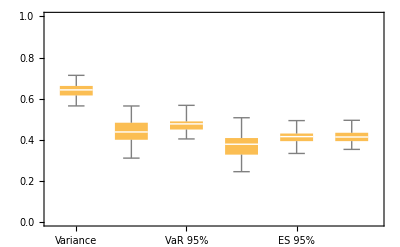

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

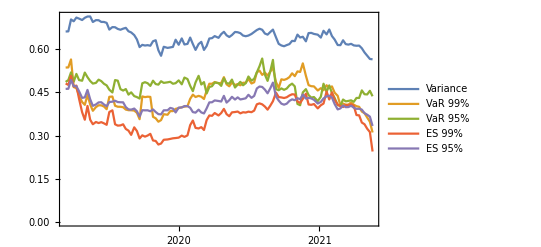

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

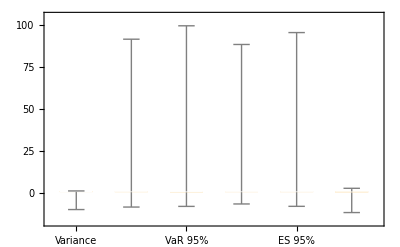

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

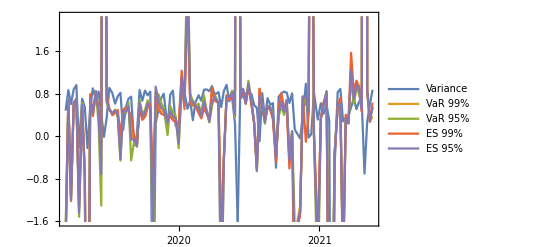

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return eth

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2019-03-11 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | eth Price | log return future | log return eth
560 | 2019-03-11 20:00:00+00:00 | 3835. | BTCJ19 Curncy | 131.352 | -0.0142397 | -0.0446202
561 | 2019-03-08 21:00:00+00:00 | 3890. | BTCJ19 Curncy | 137.346 | 0.00644748 | 0.000533029
562 | 2019-03-07 21:00:00+00:00 | 3865. | BTCJ19 Curncy | 137.273 | 0.00648932 | 0.00225657
563 | 2019-03-06 21:00:00+00:00 | 3840. | BTCJ19 Curncy | 136.963 | 0.00260756 | -0.000446517
564 | 2019-03-05 21:00:00+00:00 | 3830. | BTCJ19 Curncy | 137.024 | 0.0358842 | 0.0798305
565 | 2019-03-04 21:00:00+00:00 | 3695. | BTCJ19 Curncy | 126.511 | -0.0332699 | -0.071371
566 | 2019-03-01 21:00:00+00:00 | 3820. | BTCJ19 Curncy | 135.87 | 0.0078844 | 0.000831015
567 | 2019-02-28 21:00:00+00:00 | 3790. | BTCH19 Curncy | 135.757 | 0.0213341 | 0.0347623
568 | 2019-02-27 21:00:00+00:00 | 3710. | BTCH19 Curncy | 131.119 | -0.0173685 | -0.027971)

```mathematica
hvec
```

{{2019-03-11},{1.11761},{1.16308},{1.13689},{1.24022},{1.20655},{1.06741},{{0.09432647305380173, {h$234417873 -> 1.1630781068478286}},{0.06020578600566211, {h$234417873 -> 1.136886054375963}},{0.11252981196467511, {h$234417873 -> 1.240223569628828}},{0.08134796843627268, {h$234417873 -> 1.2065524233417886}},{0.05984725068270993, {h$234417873 -> 1.0674092224996623}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

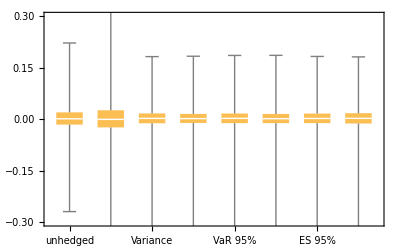

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

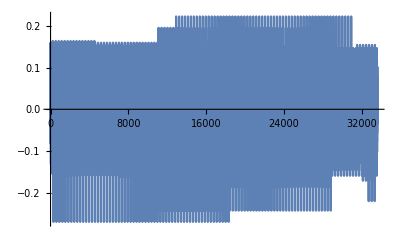

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

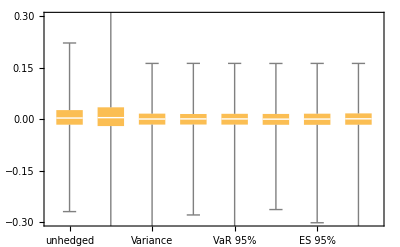

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

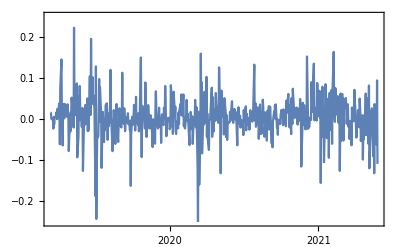
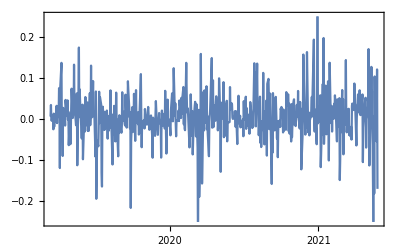

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

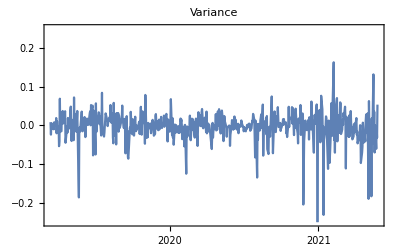
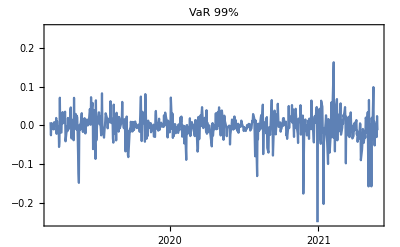
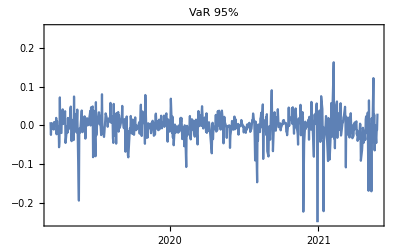
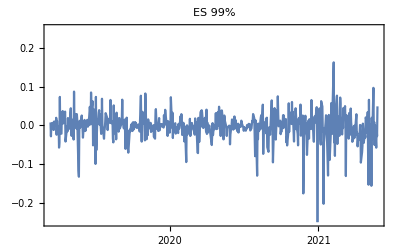
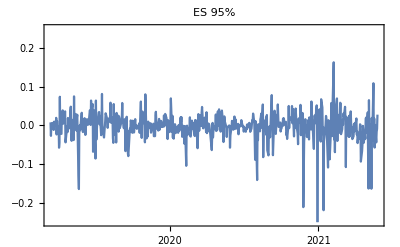
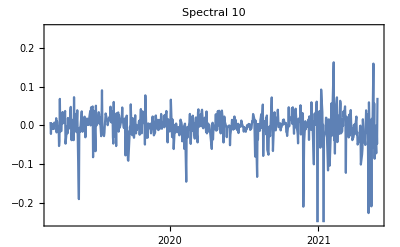

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

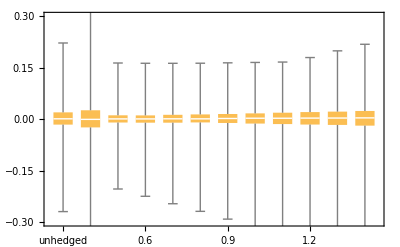

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

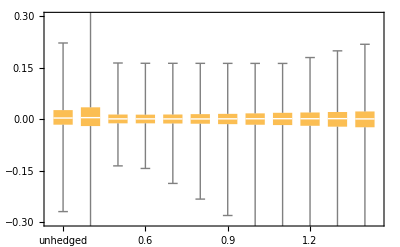

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 1.01343 | 0.58111 | 0.857613 | 0.983244 | 0.840619 | 1.13318
2021-05-13 | 0.960865 | 0.80506 | 0.914637 | 0.796049 | 0.851772 | 1.09701
2021-05-06 | 0.972534 | 0.813718 | 0.893602 | 0.804579 | 0.852111 | 1.1302
2021-04-29 | 0.98093 | 0.836108 | 0.887296 | 0.815936 | 0.861401 | 1.14146
2021-04-22 | 0.994424 | 0.825792 | 0.918792 | 0.815936 | 0.872172 | 1.16005
2021-04-15 | 1.01408 | 0.850906 | 0.881421 | 0.98879 | 0.931212 | 1.10363
2021-04-08 | 1.01441 | 0.851728 | 0.881367 | 0.991964 | 0.931317 | 1.10248
2021-04-01 | 1.01348 | 0.928935 | 0.875371 | 1.17859 | 0.997882 | 1.07795
2021-03-25 | 1.01772 | 0.960644 | 0.944217 | 1.17227 | 1.00003 | 1.06463
2021-03-18 | 1.0214 | 0.937982 | 0.88347 | 1.18606 | 1.00002 | 1.08546
2021-03-11 | 1.01661 | 0.943254 | 0.879545 | 1.18812 | 0.99886 | 1.07053
2021-03-04 | 1.02308 | 0.946103 | 1.00697 | 1.13507 | 1.0025 | 1.08797
2021-02-25 | 1.01058 | 0.951622 | 0.877186 | 1.17992 | 0.997275 | 1.06532
2021-02-18 | 1.01291 | 0.930273 | 0.873312 | 1.15423 | 1.00273 | 1.05905
2021-02-10 | 1.02906 | 0.978124 | 0.85165 | 1.15901 | 1.01032 | 1.06713
2021-02-03 | 1.06049 | 0.935638 | 0.977442 | 1.22434 | 1.03624 | 1.08481
2021-01-27 | 1.07693 | 0.911514 | 1.02323 | 1.03074 | 1.02104 | 1.12142
2021-01-20 | 1.06466 | 0.947902 | 0.875926 | 1.22289 | 1.03258 | 1.10147
2021-01-12 | 1.06725 | 0.963399 | 1.03226 | 0.961678 | 1.023 | 1.18314
2021-01-05 | 1.05605 | 0.881466 | 1.04114 | 0.865188 | 0.932409 | 1.27888
2020-12-28 | 1.00167 | 0.896718 | 1.05279 | 0.864297 | 0.94263 | 1.09612
2020-12-18 | 0.995396 | 0.878782 | 1.04103 | 0.87103 | 0.95318 | 1.12511
2020-12-11 | 1.01092 | 0.917071 | 1.04115 | 0.873957 | 1.00727 | 1.07687
2020-12-04 | 1.01164 | 0.919016 | 1.0421 | 0.876637 | 1.00273 | 1.0715
2020-11-27 | 0.998605 | 1.07422 | 0.917381 | 1.34301 | 1.09559 | 0.953154
2020-11-19 | 1.0077 | 0.871089 | 1.09542 | 0.868587 | 1.03988 | 1.03448
2020-11-12 | 1.00838 | 0.978381 | 1.04088 | 1.08356 | 1.03255 | 0.963965
2020-11-05 | 1.00531 | 0.991761 | 1.04777 | 1.07319 | 1.03298 | 1.00404
2020-10-29 | 0.993163 | 1.08562 | 0.923421 | 1.31812 | 1.05982 | 0.925669
2020-10-22 | 0.993882 | 1.12447 | 0.934877 | 1.31937 | 1.06328 | 0.933052
2020-10-15 | 0.984032 | 1.05708 | 0.912587 | 1.3131 | 1.0597 | 0.941394
2020-10-08 | 0.970076 | 1.04567 | 0.905138 | 1.30144 | 1.03139 | 0.913947
2020-10-01 | 0.962748 | 1.04379 | 0.865147 | 1.29861 | 1.02562 | 0.914875
2020-09-24 | 0.962555 | 1.0414 | 0.90768 | 1.27847 | 1.02294 | 0.913888
2020-09-17 | 0.96727 | 1.07117 | 0.905325 | 1.30384 | 1.05017 | 0.888783
2020-09-10 | 0.977674 | 1.06356 | 0.902433 | 1.30889 | 1.04971 | 0.896422
2020-09-02 | 0.924958 | 0.856609 | 1.04483 | 0.850363 | 0.951334 | 0.906637
2020-08-26 | 0.88765 | 0.854725 | 0.944987 | 0.835538 | 0.919063 | 0.904011
2020-08-19 | 0.874424 | 0.832653 | 0.920054 | 0.831974 | 0.910674 | 0.886923
2020-08-12 | 0.87069 | 0.840359 | 0.936493 | 0.835488 | 0.901373 | 0.876845
2020-08-05 | 0.874315 | 0.834461 | 0.954364 | 0.824467 | 0.917248 | 0.88803
2020-07-29 | 0.867464 | 0.845089 | 0.941121 | 0.838935 | 0.906036 | 0.857346
2020-07-22 | 0.873058 | 0.850357 | 0.932659 | 0.84871 | 0.919091 | 0.855967
2020-07-15 | 0.848437 | 0.835967 | 0.914887 | 0.831566 | 0.909689 | 0.797835
2020-07-08 | 0.845201 | 0.824025 | 0.911029 | 0.824629 | 0.906957 | 0.801431
2020-06-30 | 0.840007 | 0.824579 | 0.906439 | 0.811539 | 0.859094 | 0.860051
2020-06-23 | 0.838847 | 0.822083 | 0.906203 | 0.811743 | 0.887027 | 0.829951
2020-06-16 | 0.841388 | 0.822083 | 0.903782 | 0.811545 | 0.886989 | 0.83373
2020-06-09 | 0.852795 | 0.808545 | 0.905842 | 0.797432 | 0.891682 | 0.83637
2020-06-02 | 0.855568 | 0.811582 | 0.922523 | 0.805878 | 0.886741 | 0.843444
2020-05-26 | 0.853673 | 0.813044 | 0.915448 | 0.808727 | 0.908853 | 0.834782
2020-05-18 | 0.846667 | 0.817712 | 0.910218 | 0.804661 | 0.859551 | 0.87201
2020-05-11 | 0.84317 | 0.809879 | 0.902398 | 0.798275 | 0.867572 | 0.879731
2020-05-04 | 0.853194 | 0.810986 | 0.93449 | 0.800664 | 0.892125 | 0.855391
2020-04-27 | 0.877192 | 0.828868 | 0.915889 | 0.813493 | 0.881184 | 0.917033
2020-04-20 | 0.872363 | 0.819652 | 0.923171 | 0.812129 | 0.897511 | 0.882648
2020-04-13 | 0.865947 | 0.81653 | 0.906424 | 0.804019 | 0.86245 | 0.913768
2020-04-03 | 0.866389 | 0.826294 | 0.930657 | 0.805304 | 0.882416 | 0.865245
2020-03-27 | 0.866284 | 0.820951 | 0.920314 | 0.803453 | 0.886648 | 0.86199
2020-03-20 | 0.866447 | 0.821388 | 0.91647 | 0.804645 | 0.880906 | 0.867786
2020-03-13 | 0.849283 | 0.884022 | 0.901402 | 0.79422 | 0.887618 | 0.835743
2020-03-06 | 0.858763 | 0.651206 | 0.91108 | 0.611039 | 0.775044 | 0.986789
2020-02-28 | 0.913832 | 0.803077 | 0.844551 | 0.694712 | 0.796316 | 0.990067
2020-02-21 | 0.905886 | 0.678161 | 0.869831 | 0.620966 | 0.776532 | 1.01657
2020-02-13 | 0.887587 | 0.66129 | 0.85497 | 0.616559 | 0.741522 | 1.03462
2020-02-06 | 0.892168 | 0.673748 | 0.787125 | 0.708839 | 0.768414 | 1.01495
2020-01-30 | 0.898395 | 0.769484 | 0.894659 | 0.679248 | 0.775812 | 1.00759
2020-01-23 | 0.880635 | 0.733758 | 0.801095 | 0.613456 | 0.75841 | 1.00629
2020-01-15 | 0.880582 | 0.658907 | 0.804713 | 0.585436 | 0.753943 | 0.981992
2020-01-08 | 0.891711 | 0.732299 | 0.901689 | 0.643332 | 0.778284 | 0.971529
2019-12-31 | 0.87989 | 0.636905 | 0.805615 | 0.587233 | 0.760963 | 0.954454
2019-12-23 | 0.891626 | 0.688049 | 0.903503 | 0.609224 | 0.768011 | 0.940621
2019-12-16 | 0.879989 | 0.706666 | 0.897842 | 0.602464 | 0.75542 | 0.977444
2019-12-09 | 0.877848 | 0.707518 | 0.911846 | 0.599961 | 0.757346 | 0.96399
2019-12-02 | 0.883571 | 0.718591 | 0.888544 | 0.608531 | 0.753568 | 0.928456
2019-11-22 | 0.902607 | 0.715652 | 0.873003 | 0.606754 | 0.766121 | 0.981417
2019-11-15 | 0.892492 | 0.635898 | 0.866264 | 0.583304 | 0.741625 | 0.991681
2019-11-08 | 0.916948 | 0.655374 | 0.918587 | 0.577101 | 0.762596 | 0.95497
2019-11-01 | 0.944435 | 0.747748 | 0.972237 | 0.639399 | 0.833114 | 0.987189
2019-10-25 | 0.947892 | 0.753517 | 0.954473 | 0.617033 | 0.81029 | 1.03019
2019-10-18 | 0.974112 | 0.731093 | 0.924552 | 0.711178 | 0.850692 | 1.0265
2019-10-11 | 0.969452 | 0.726092 | 0.934598 | 0.697518 | 0.841281 | 1.05273
2019-10-04 | 0.966791 | 0.721834 | 0.934106 | 0.692866 | 0.84262 | 1.04398
2019-09-27 | 0.963948 | 0.733698 | 0.933356 | 0.687278 | 0.839811 | 1.04961
2019-09-20 | 0.953926 | 0.818861 | 0.897273 | 0.729291 | 0.837436 | 1.05834
2019-09-13 | 0.967805 | 0.917922 | 0.924731 | 0.770886 | 0.885189 | 1.03599
2019-09-06 | 0.980558 | 0.90515 | 0.918263 | 0.804844 | 0.89506 | 1.06134
2019-08-29 | 0.993533 | 0.844738 | 1.00544 | 0.753926 | 0.889476 | 1.06858
2019-08-22 | 0.99809 | 0.878698 | 1.0293 | 0.791163 | 0.917265 | 1.01687
2019-08-15 | 1.00808 | 0.860222 | 0.980344 | 0.820095 | 0.936559 | 1.06856
2019-08-08 | 1.00779 | 0.880112 | 0.932757 | 0.824317 | 0.920574 | 1.07567
2019-08-01 | 1.01279 | 0.869416 | 0.933336 | 0.82171 | 0.925767 | 1.07544
2019-07-25 | 1.01973 | 0.89477 | 0.98072 | 0.800456 | 0.921943 | 1.06948
2019-07-18 | 1.02641 | 0.914701 | 0.988651 | 0.809279 | 0.930572 | 1.07107
2019-07-11 | 1.02758 | 1.01836 | 1.00075 | 0.917915 | 1.00641 | 1.07448
2019-07-03 | 1.02547 | 0.994509 | 0.992307 | 0.906575 | 0.980081 | 1.06177
2019-06-26 | 1.12678 | 1.0062 | 1.07893 | 0.87107 | 1.01642 | 1.21804
2019-06-19 | 1.16238 | 1.00729 | 1.20711 | 0.912703 | 1.07372 | 1.20815
2019-06-12 | 1.17449 | 1.02718 | 1.24303 | 0.931304 | 1.07887 | 1.21552
2019-06-05 | 1.17626 | 1.01302 | 1.24653 | 0.899363 | 1.07867 | 1.18591
2019-05-29 | 1.18742 | 1.09001 | 1.24964 | 0.936988 | 1.08752 | 1.2205
2019-05-21 | 1.18835 | 1.09734 | 1.25258 | 0.96041 | 1.11985 | 1.20199
2019-05-14 | 1.19175 | 1.02486 | 1.22764 | 0.952667 | 1.09653 | 1.21087
2019-05-07 | 1.22997 | 1.2374 | 1.21121 | 1.11458 | 1.20893 | 1.225
2019-04-30 | 1.21258 | 1.13128 | 1.21777 | 1.04689 | 1.20677 | 1.18721
2019-04-23 | 1.17254 | 1.21128 | 1.22913 | 1.06243 | 1.15692 | 1.18003
2019-04-15 | 1.17396 | 1.09985 | 1.18405 | 1.11192 | 1.15443 | 1.22139
2019-04-08 | 1.16331 | 1.12787 | 1.21563 | 1.16225 | 1.18325 | 1.12968
2019-04-01 | 1.16444 | 1.18928 | 1.19736 | 1.20905 | 1.21239 | 1.16012
2019-03-25 | 1.14167 | 1.18465 | 1.21753 | 1.25422 | 1.23317 | 1.07598
2019-03-18 | 1.11546 | 1.13567 | 1.16349 | 1.23208 | 1.21639 | 1.0633
2019-03-11 | 1.11761 | 1.16308 | 1.13689 | 1.24022 | 1.20655 | 1.06741)

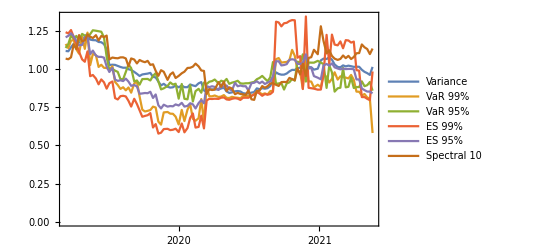

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```